```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_,k_]:=P[n,k]=Sum[ K[j]P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
Phyp[n_,k_,a_]:=Phyp[n,k,a]=Sum[If[K[m]==0,0,Binomial[k,j] K[m]^(k-j)Phyp[Floor[n/(m^(k-j))],j,m+1]],{m,a,n^(1/k)},{j,0,k-1}]
Phyp[n_,1,a_]:=Phyp[n,1,a]=Sum[ K[j],{j,a,n}];Phyp[n_,0,a_]:=1
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
P1[n_,z_]:=Expand[Sum[bins[z,a]P[n,a],{a,0,Log[2,n]}]]
P1h[n_,z_]:=Expand[Sum[bins[z,a]Phyp[n,a,2],{a,0,Log[2,n]}]]
P1h2[n_,z_] := Expand[FullSimplify[(P1h[n,z+1]-1)/(z+1)]]
```

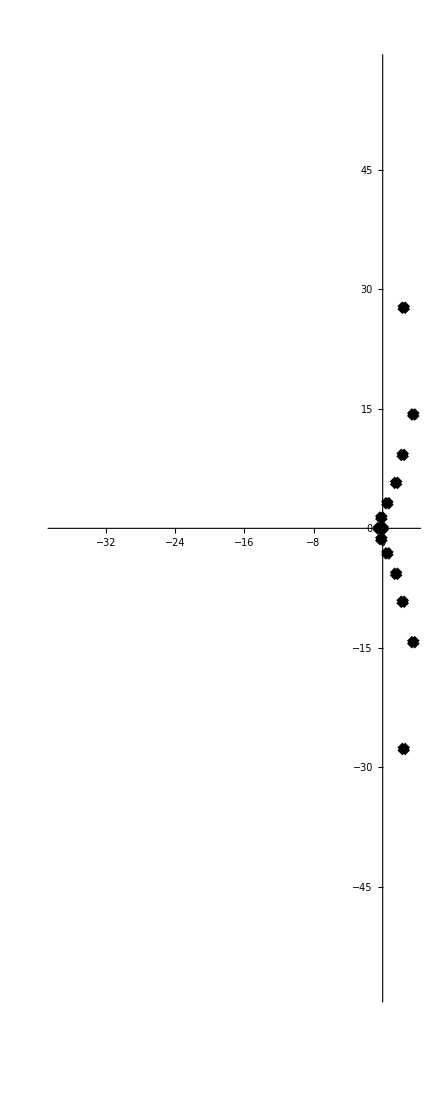

```mathematica
RootLocusPlot[1/Expand[P1h[530000,x]],{k,0,1},FeedbackType->None]
```

```mathematica
(1-1/List@@NRoots[ P1h[530000,x]==0,x][[All,2]])
```

{1.0078,1.00032-0.00166572 ⅈ,1.00032+0.00166572 ⅈ,1.00244-0.0131344 ⅈ,1.00244+0.0131344 ⅈ,3.33346,1.08156-0.729614 ⅈ,1.08156+0.729614 ⅈ,8826.48,0.946785-0.308571 ⅈ,0.946785+0.308571 ⅈ,0.955564-0.163063 ⅈ,0.955564+0.163063 ⅈ,0.974388-0.102019 ⅈ,0.974388+0.102019 ⅈ,0.996852-0.0358172 ⅈ,0.996852+0.0358172 ⅈ,0.983653-0.0658927 ⅈ,0.983653+0.0658927 ⅈ}

```mathematica
P1[100,z]
```

1+(341 z)/72+(6683 z^2)/360+(45 z^3)/16+(41 z^4)/18+(2 z^5)/15+(7 z^6)/720

```mathematica
vv:= {-999.8815576256916,-182.67217231000708,-1.4793791531870175-27.308662724086556 ⅈ,-1.4793791531870175+27.308662724086556 ⅈ,-0.6706279346947679-0.5389419630736445 ⅈ,-0.6706279346947679+0.5389419630736445 ⅈ,-0.0031680220240090963,0.10809074763072718-2.5030341283517754 ⅈ,0.10809074763072718+2.5030341283517754 ⅈ,0.7555329045665851-5.580324806796909 ⅈ,0.7555329045665851+5.580324806796909 ⅈ,1.0648324145458472-9.82455476742625 ⅈ,1.0648324145458472+9.82455476742625 ⅈ}
```

```mathematica
Product[ 1-1/j,{j,vv}]
```

1459.1+0. ⅈ

```mathematica
N[P1h[530000,1]]
```

43903.9

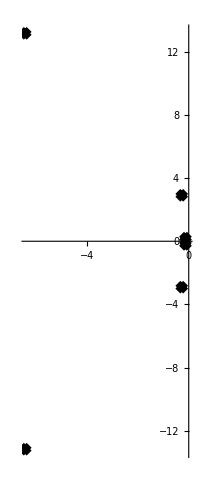

```mathematica
RootLocusPlot[1/Expand[P1h[100,x]],{k,0,1},FeedbackType->None]
```